```mathematica
stokeslet[x_,e_]:= 3/400 (e+Dot[x,e]x/Norm[x]^2)/Norm[x];
dipole[x_,d_,e_]:= 3/400((Dot[x,d]e-Dot[e,x]d-Dot[d,e]x)/Norm[x]+(3Dot[e,x]Dot[d,x]x)/Norm[x]^3)/Norm[x]^2;
doublet[x_,e_]:=3/400(-e+3Dot[e,x]x/Norm[x]^2)/Norm[x]^3;blakelet[x_,y_,e_]:= stokeslet[y-x,e]+(-stokeslet[y-(x-{0,2 x[[2]]}),{1,0}] +2x[[2]]dipole[y-(x-{0,2 x[[2]]}),{1,0},{0,1}]-2x[[2]]^2 doublet[y-(x-{0,2 x[[2]]}),{1,0}])e[[1]] + (-stokeslet[y-(x-{0,2 x[[2]]}),{0,1}] +2x[[2]]dipole[y-(x-{0,2 x[[2]]}),{0,1},{0,1}]-2x[[2]]^2 doublet[y-(x-{0,2 x[[2]]}),{0,1}])e[[2]];
```

```mathematica
xx[t_]={Cos[t-Pi/2],Sin[t-Pi/2]+2};
xx[0]
```

{0,1}

```mathematica
xxdot[t_]=N[D[xx[t],t]];
```

```mathematica
f[y_,t_]=blakelet[xx[t],y,xxdot[t]];
f2[y1_,y2_,t_]=blakelet[xx[t],{y1,y2},xxdot[t]];
```

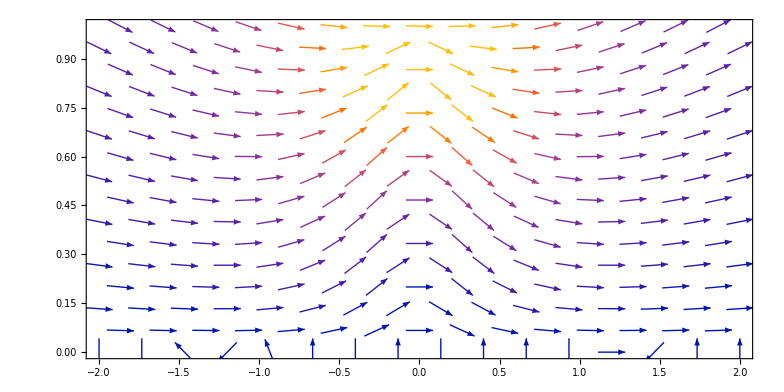

```mathematica
VectorPlot[f2[x1,x2,0],{x1,-2,2},{x2,0,1},PlotRange->{{-2,2},{0,1}},AspectRatio->1/2]
```

```mathematica
f2[1,0,0]
```

{0,0}

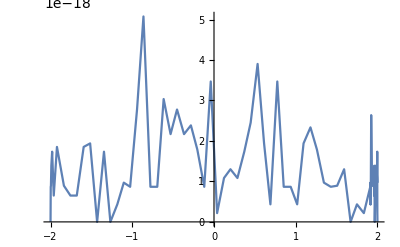

```mathematica
Plot[Norm[f2[x,0.00,0]],{x,-2,2}]
```

```mathematica
{yy1,yy2}=NDSolveValue[{{y1'[t],y2'[t]}==f2[y1[t],y2[t],t],y1[0]==1,y2[0]==0},{y1,y2},{t,0,2Pi}];
```

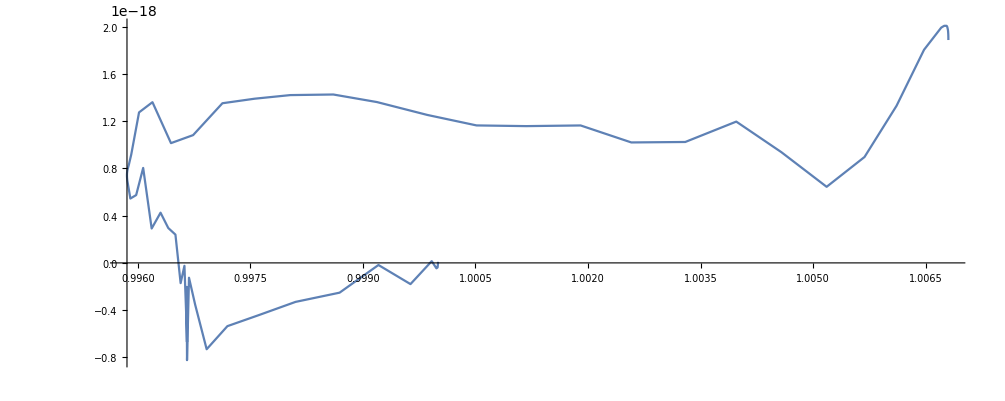

```mathematica
ParametricPlot[{yy1[t],yy2[t]},{t,0,2Pi}]
```

```mathematica
tracer=ParametricNDSolveValue[{{y11'[t],y22'[t]}==f2[y11[t],y22[t],t],y11[0]==b1,y22[0]==b2},{y11[2Pi]-y11[0],y22[2Pi]-y22[0]},{t,0,2Pi},{b1,b2},Method->"ImplicitRungeKutta",PrecisionGoal->15];
```

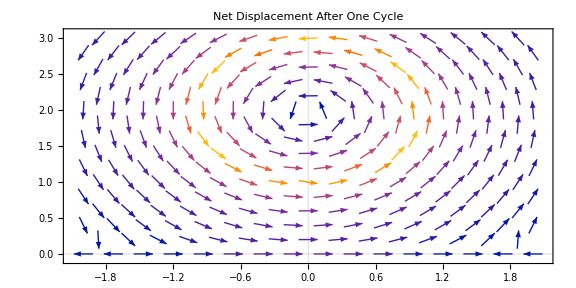

```mathematica
VectorPlot[tracer[p,q],{p,-2,2},{q,0,3},PlotTheme->"Scientific",PlotLabel->"Net Displacement After One Cycle",AspectRatio->1/2,ImageSize->Large,PlotLegends->Automatic]
```

```mathematica
tracer[1,0]
```

{0.00680225,1.76639×10^-18}

```mathematica
stokeslet2[x_,y_,e_]:= 3/40 (e+Dot[y-x,e](y-x)/Norm[y-x]^2)/Norm[y-x];
g[y_,t_]=stokeslet2[xx[t],y,xxdot[t]];
g2[y1_,y2_,t_]=stokeslet2[xx[t],{y1,y2},xxdot[t]];
```

```mathematica
tracer2=ParametricNDSolveValue[{{y111'[t],y222'[t]}==stokeslet2[xx[t],{y111[t],y222[t]},xxdot[t]],y111[0]==c1,y222[0]==c2},{y111[2Pi]-y111[0],y222[2Pi]-y222[0]},{t,0,2Pi},{c1,c2}];
tracer2[1,1]
```

{0.157574,0.225164}

```mathematica
VectorPlot[tracer2[p,q],{p,-15,15},{q,0,10},PlotTheme->"Scientific",PlotLabel->"Net Displacement After One Cycle",AspectRatio->1/2,ImageSize->Large];
```

```mathematica
{yyy1,yyy2}=NDSolveValue[{{y111'[t],y222'[t]}==stokeslet2[xx[t],{y111[t],y222[t]},xxdot[t]],y111[0]==1,y222[0]==1},{y111,y222},{t,0,2Pi},Method->StiffnessSwitching];
```

```mathematica
ParametricPlot[{yyy1[t],yyy2[t]},{t,0,2Pi}];
```

```mathematica
approxlet[a_,b_,c_] := (3/400) (-(Dot[a,c]a /(Norm[a]^2) - (1/Dot[a,a])(1-(2Dot[a,{0,b[[2]]}]/(Dot[a,a]))Dot[a+{0,2b[[2]]},c](a+{0,2b[[2]]})))  +(2b[[2]]/(Norm[a]^3))(1-(6Dot[a,{0,b[[2]]}]/Dot[a,a]))(Dot[a+{0,2b[[2]]},{0,1}]{1,0}c[[1]]-Dot[a+{0,2b[[2]]},{1,0}]{0,1}c[[1]]-(a+{0,2b[[2]]})c[[2]])-6b[[2]]/Norm[a]^5 (1-10 Dot[a+2b[[2]],{0,b[[2]]}]/Dot[a,a])((a+{0,2b[[2]]})[[1]](a+{0,2b[[2]]})[[2]](a+{0,2b[[2]]}) c[[1]]-(a+{0,2b[[2]]})[[1]](a+{0,2b[[2]]})[[2]](a+{0,2b[[2]]}) c[[2]]))
approxlet[p,q,r]
```

Part::partd: Part specification q⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{3/400 ((1-(2 p p.{0,q⟦2⟧} {p,p+2 q⟦2⟧}.r)/(p.p))/(p.p)-(p p.r)/Norm[p]^2+(2 (1-(6 p.{0,q⟦2⟧})/(p.p)) q⟦2⟧ ((p+2 q⟦2⟧) r⟦1⟧-p r⟦2⟧))/Norm[p]^3-(6 (1-(10 (p+2 q⟦2⟧).{0,q⟦2⟧})/(p.p)) q⟦2⟧ (p^2 (p+2 q⟦2⟧) r⟦1⟧-p^2 (p+2 q⟦2⟧) r⟦2⟧))/Norm[p]^5),3/400 (-(p p.r)/Norm[p]^2+(1-(2 p.{0,q⟦2⟧} {p,p+2 q⟦2⟧}.r (p+2 q⟦2⟧))/(p.p))/(p.p)+(2 (1-(6 p.{0,q⟦2⟧})/(p.p)) q⟦2⟧ (-p r⟦1⟧-(p+2 q⟦2⟧) r⟦2⟧))/Norm[p]^3-(6 (1-(10 (p+2 q⟦2⟧).{0,q⟦2⟧})/(p.p)) q⟦2⟧ (p (p+2 q⟦2⟧)^2 r⟦1⟧-p (p+2 q⟦2⟧)^2 r⟦2⟧))/Norm[p]^5)}

```mathematica
"Integrate[-approxlet[{p,q},xx[t],xxdot[t]],{t,0,2Pi}];"
```

```mathematica
Integrate[-approxlet[{p,q},xx[t],xxdot[t]],{t,0,2Pi}]
```

{-(3 π (q^2+p^2 (1+q)+(3 p^2 (8+q) (p^2+q^2) (-190+p^2-40 q+q^2))/((Abs[p]^2+Abs[q]^2)^(5/2))-((p^2+q^2) (p^2 (8+q)+q (-153-16 q+q^2)))/((Abs[p]^2+Abs[q]^2)^(3/2))))/(200 (p^2+q^2)^2),-(3 π (p^2+q^2+p q (8+q)+(3 p (p^2+q^2) (-8850+p^2 (51+q (16+q))+q (-4560+q (-714+(-24+q) q))))/((Abs[p]^2+Abs[q]^2)^(5/2))+(p (p^2+(-24+q) q) (p^2+q^2))/((Abs[p]^2+Abs[q]^2)^(3/2))))/(200 (p^2+q^2)^2)}

```mathematica
f[p_,q_]:={-(3 π (q^2+p^2 (1+q)+(3 p^2 (8+q) (p^2+q^2) (-190+p^2-40 q+q^2))/((Abs[p]^2+Abs[q]^2)^(5/2))-((p^2+q^2) (p^2 (8+q)+q (-153-16 q+q^2)))/((Abs[p]^2+Abs[q]^2)^(3/2))))/(200 (p^2+q^2)^2),-(3 π (p^2+q^2+p q (8+q)+(3 p (p^2+q^2) (-8850+p^2 (51+q (16+q))+q (-4560+q (-714+(-24+q) q))))/((Abs[p]^2+Abs[q]^2)^(5/2))+(p (p^2+(-24+q) q) (p^2+q^2))/((Abs[p]^2+Abs[q]^2)^(3/2))))/(200 (p^2+q^2)^2)}
errorf[p_,q_] = Norm[tracer[p,q]-f[p,q]];
```

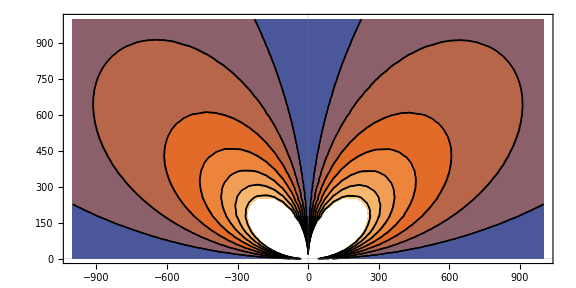

```mathematica
ContourPlot[errorf[p,q],{p,-1000,1000},{q,0,1000},PlotTheme->"Scientific",AspectRatio->1/2,PlotLegends->Automatic,ImageSize->Large]
```

```mathematica
$Aborted
```

$Aborted

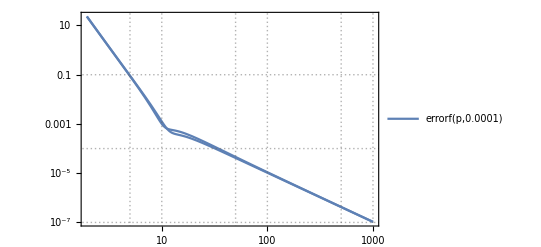

```mathematica
LogLogPlot[{errorf[p,0.0001]},{p,-1000,1000},PlotTheme->"Detailed"]
```

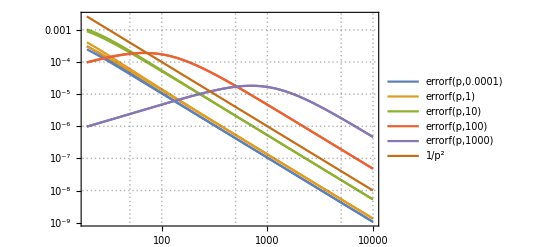

```mathematica
LogLogPlot[{errorf[p,0.0001],errorf[p,1],errorf[p,10],errorf[p,100],errorf[p,1000],p^(-2)},{p,-10000,10000},PlotTheme->"Detailed"]
```

```mathematica
-Graphics-\
```

ParametricNDSolveValue::prange: Invalid non-numeric value -p for parameter b2.

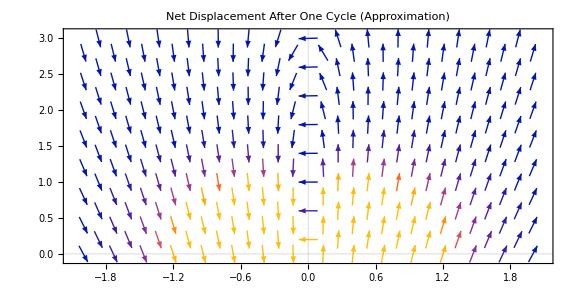

```mathematica
VectorPlot[f[p,q],{p,-2,2},{q,0,3},PlotTheme->"Scientific",PlotLabel->"Net Displacement After One Cycle (Approximation)",AspectRatio->1/2,ImageSize->Large,PlotRange->All,PlotLegends->Automatic]
```

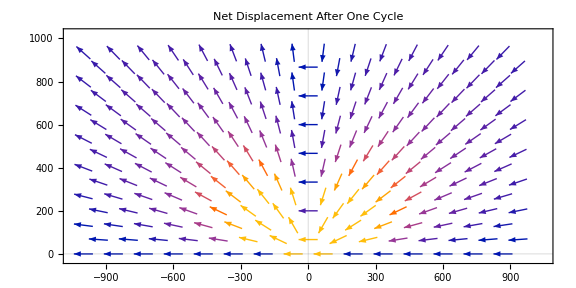
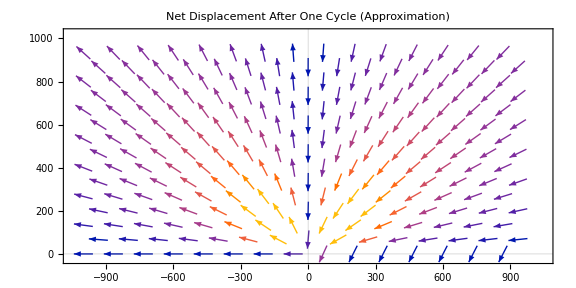

Null -Graphics- -Graphics-

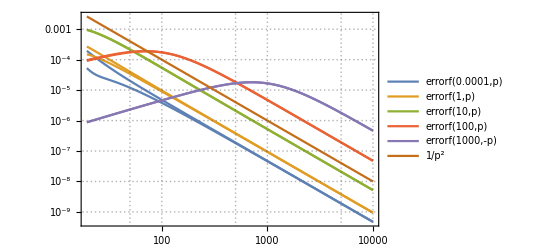

```mathematica
LogLogPlot[{errorf[0.0001,p],errorf[1,p],errorf[10,p],errorf[100,p],errorf[1000,-p],p^(-2)},{p,-10000,10000},PlotTheme->"Detailed"]
```